```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\GitHub\collab-optimizer\data

```mathematica
ClearAll[dat]
```

```mathematica
dat[2,.1]=<<task_alloc_2_0.1.txt;
dat[2,1]=<<task_alloc_2_1.0.txt;
dat[2,10]=<<task_alloc_2_10.0.txt;
```

```mathematica
dat[3,.1]=<<task_alloc_3_0.1.txt;
dat[3,1]=<<task_alloc_3_1.0.txt;
dat[3,10]=<<task_alloc_3_10.0.txt;
```

```mathematica
dat[4,.1]=<<task_alloc_4_0.1.txt;
dat[4,1]=<<task_alloc_4_1.0.txt;
dat[4,10]=<<task_alloc_4_10.0.txt;
```

```mathematica
dat[5,.1]=<<task_alloc_5_0.1.txt;
dat[5,1]=<<task_alloc_5_1.0.txt;
dat[5,10]=<<task_alloc_5_10.0.txt;
```

```mathematica
dat[6,.1]=<<task_alloc_6_0.1.txt;
dat[6,1]=<<task_alloc_6_1.0.txt;
dat[6,10]=<<task_alloc_6_10.0.txt;
```

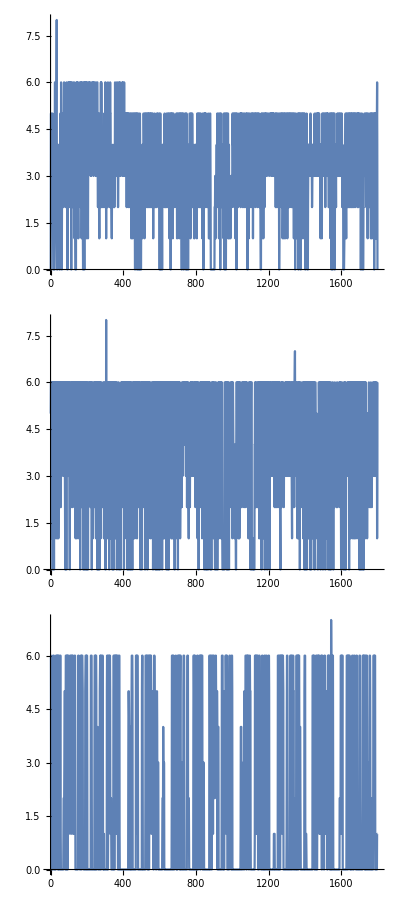

```mathematica
Column[ListLinePlot[dat[2,#],AspectRatio->1/5,ImageSize->Large]&/@{.1,1,10}]
```

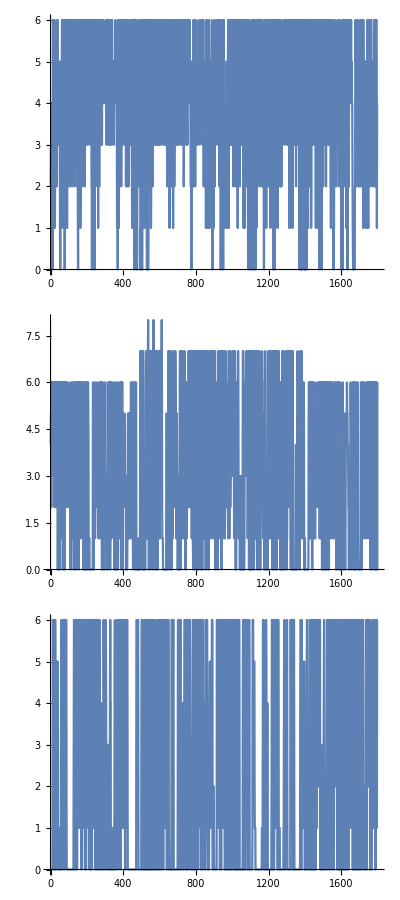

```mathematica
Column[ListLinePlot[dat[3,#],AspectRatio->1/5,ImageSize->Large]&/@{.1,1,10}]
```

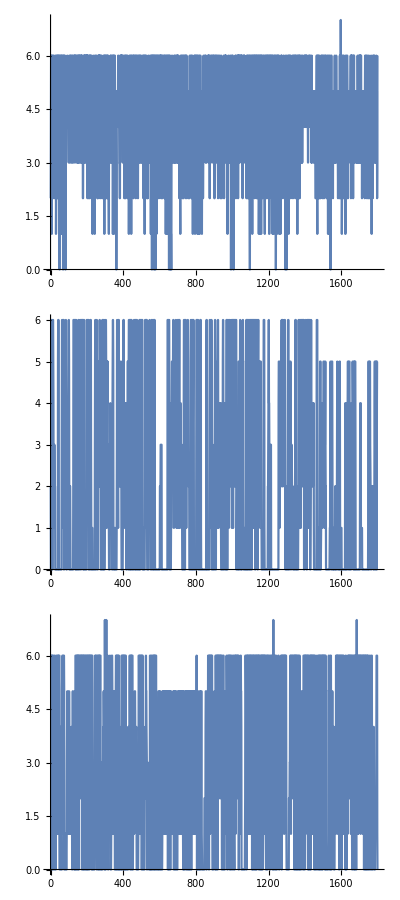

```mathematica
Column[ListLinePlot[dat[4,#],AspectRatio->1/5,ImageSize->Large]&/@{.1,1,10}]
```

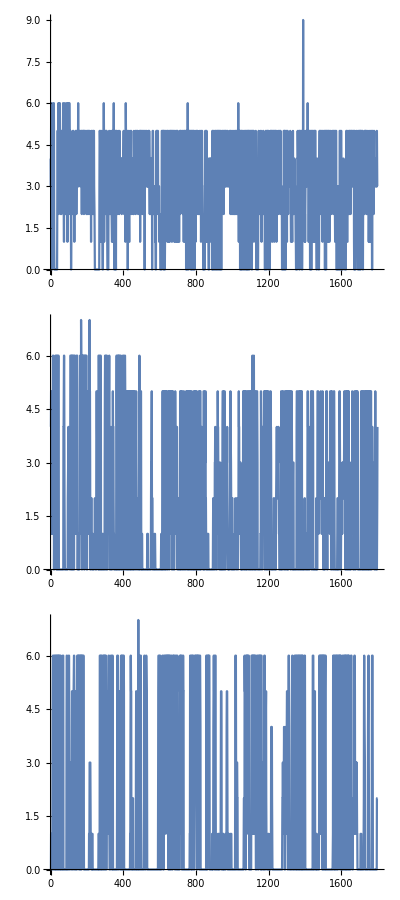

```mathematica
Column[ListLinePlot[dat[5,#],AspectRatio->1/5,ImageSize->Large]&/@{.1,1,10}]
```

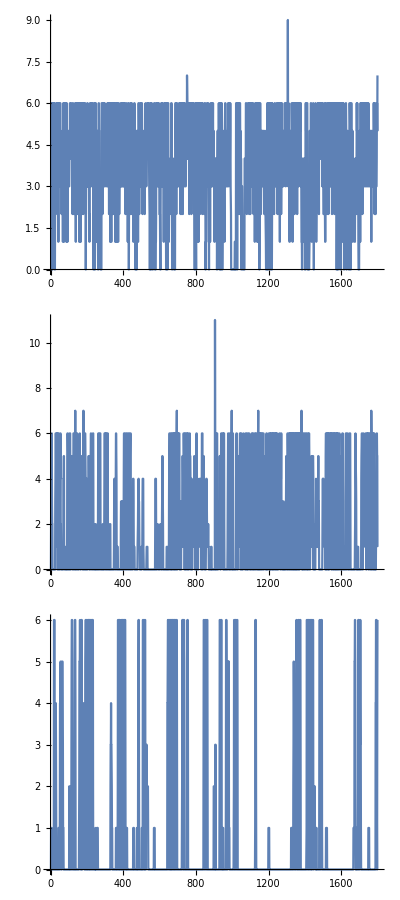

```mathematica
Column[ListLinePlot[dat[6,#],AspectRatio->1/5,ImageSize->Large]&/@{.1,1,10}]
```